### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/Using Indivaria

### Keywords

Details

Sompob Saralamba

Sompob Saralamba

# Using Indivaria

Indivaria is a package which collected some published mathematical models for the dynamics of malaria paraistes in an infected patient during treatment and without treatment with antimalarial drug. IDVL is the main function of the package. The user has to enter the list of the parameters and their values of the model they choose in an input file. The parameters of each model are different and can be shown by using the fucntion ListPar.

IDVL["inputfile"] | performs the calculation of the model following the parameters in the input file.
ListPar[modelID,outform] | shows the list of parameters required by the model.
RI[ec50,emax,gamma,const] | calculates the resistance index.

XXXX.

inputfile is the name of the input file. The input file is the text file which user can create and edit by using text editor like Notepad or Vim. The following is the example of the input file. There must be the spaces between the name of parameter, its value and the comment.

```mathematica
# the example of the input file for the model 1.1 ("mod1_1.in").
model        1.1
initN	    6.02*10^11	# initial number of parasites
lifecycle	48   # the life cycle of parasites 
mu           13   # mean age of parasites on admission
sigma	    8    # SD of the age of parasites  
pmr          12   # parasite multiplication rate
everyH       24   # duration (hours) of giving the drug
Ndrug 	   7	# number of the drug
Concfile 	"P002.csv"  # the name of DHA concentration file	
parafile 	"paraP002.csv"  # the name of parasite count file
KillZone 	{{6, 20}, {21, 38}, {39, 44}}  # the age ranges of the sensitive parasites 
gamma	    {8.31521, 3.96412, 3.96412}		# the slopes of the EC curves
ec50	     {38.2193, 0.662235, 0.662235}	# the EC50 for each kill zone
emin 	    {0.0, 0.0, 0.0}		# minimum efficacy of the drug
emax 	    {99.9779, 99.99, 99.99} 	# maximum efficacy of the drug
1/alpha	  7.78339   # the action time (hours) 
outform	  1     # output forms; check the manual for more details
```

The example of using the package. The package first must be loaded by using Needs or Get function.

```mathematica
<<Indivaria`
```

This example shows the output of IDVL from reading the input file, mod1_1.in, which has the parameters and their values as shown above.

******INDIVARIA*****

model: 1.1

outform: 1

********************

model: 1.1

parafile: paraP002.csv

concfile: P002.csv

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

killzone: {{6,20},{21,38},{39,44}}

everyh: 24

ndrug: 7

gamma: {8.31521,3.96412,3.96412}

ec50: {38.2193,0.662235,0.662235}

emin: {0.0,0.0,0.0}

emax: {99.9779,99.99,99.99}

1/alpha: 7.78339

outform: 1

runmax: 96

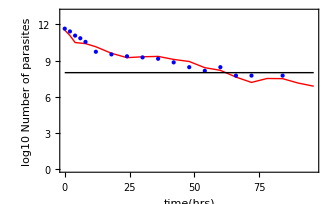

```mathematica
IDVL["mod1_1.in"]
```

The list of parameters required by the model 1.1 with outform=1 can be shown by using the function ListPar.

```mathematica
ListPar[1.1,1]
```

{model,parafile,concfile,initn,pmr,mu,sigma,lifecycle,killzone,everyh,ndrug,gamma,ec50,emin,emax,1/alpha,outform}

The detail of each model can be found at http://mice.tropmedres.ac or http://slphyx.sakngoi.com.

More About

List of models

Related Tutorials

Related Wolfram Education Group Courses